## convergence regions System1 Σ_1

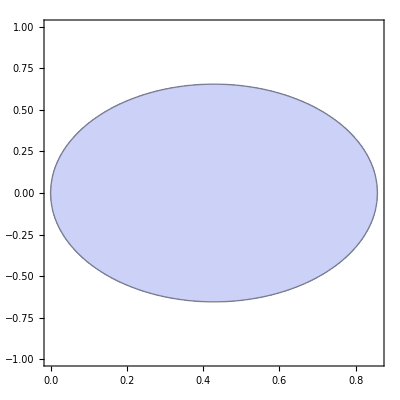

```mathematica
Sys1PIdentity= c>0and 7 c-6<0and 2 c^2 w^2-3 w^2-7 c^2+6 c>0;
plotpgf=RegionPlot[{Sys1PIdentity},{c,0,6/7},{w,-1,1}]
```

```mathematica
Sys1P1P3eq4 = c>0&&c<Root[49 c^2+48 #^2 c-168 c+24 #^4-168 #^2+144&,2]
```

c>0&&c<Root[144-168 c+49 c^2+(-168+48 c) #1^2+24 #1^4&,2]

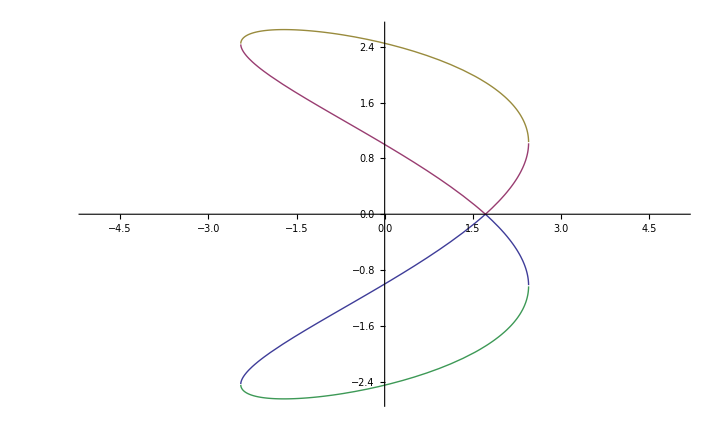

```mathematica
Plot[{Root[144-168 c+49 c^2+(-168+48 c) #1^2+24 #1^4&,2],Root[144-168 c+49 c^2+(-168+48 c) #1^2+24 #1^4&,3],Root[144-168 c+49 c^2+(-168+48 c) #1^2+24 #1^4&,4],Root[144-168 c+49 c^2+(-168+48 c) #1^2+24 #1^4&,1]},{c,-5,5}]
```

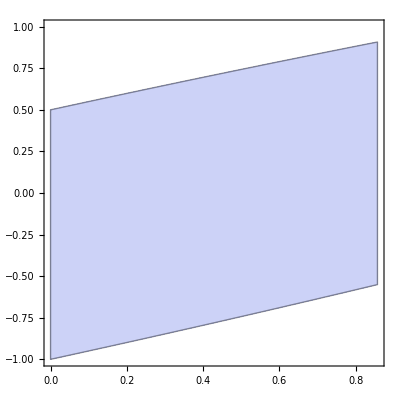

```mathematica
Sys1P2= 7 c^2-24 w c-6 c+24 w^2+12 w-12<0and c>0and 7 c-6<0;
plotpgf=RegionPlot[{Sys1P2},{c,0,6/7},{w,-1,1}]
```

## convergence regions System2 Σ_2

c≥0&&-3+2 c≤0&&-12-3 c+2 c^2+12 w-12 c w+24 w^2≤0

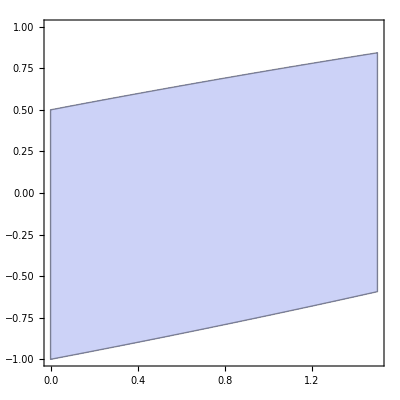

```mathematica
Sys2P2=c≥0&& 2 c-3≤0&& 2 c^2-12 w c-3 c+24 w^2+12 w-12≤0
plotpgf=RegionPlot[{Sys2P2},{c,0,1.5},{w,-1,1}]
Reduce[Sys2P2,{c,w}];
```

c≥0&&2 c≤3&&2 w^2≤1&&-3 c+2 c^2+3 w^2-c^2 w^2≤0

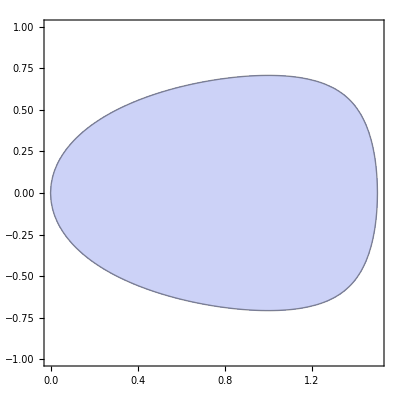

```mathematica
Sys2PIdentity = c≥0&&2 c≤3&&2 w^2≤1&&-c^2 *w^2+2*c^2+3*w^2-3*c ≤0
plotpgf=RegionPlot[{Sys2PIdentity},{c,0,1.5},{w,-1,1}]
```

c>0&&-3+c+3 w^2<0&&-9+6 c-c^2+12 w^2-3 c w^2-3 w^4≤0

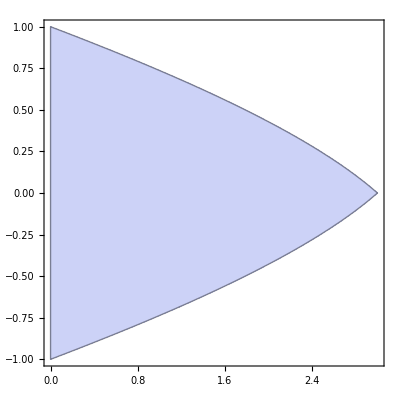

```mathematica
Sys2P1P3 = c>0&& 3*w^2+c-3<0&&-3*w^4-3*w^2*c-c^2+12*w^2+6*c-9≤ 0
plotpgf=RegionPlot[{Sys2P1P3},{c,0,3},{w,-1,1}]
```